```mathematica
(* spherical to carteisan coordinates - useful for parameterizing unit vectors *)
s2c[Φ_,Θ_]:={ Cos[Θ] Sin[Φ], Sin[Φ] Sin[Θ],Cos[Φ]};
```

```mathematica
a={1,0,0};b={-1/2,0,√3/2}; c={-1/2,0,-√3/2};
```

```mathematica
A={{a[[3]],a[[1]]-I a[[2]]},{a[[1]]+I a[[2]],-a[[3]]}}
```

(0 | 1
1 | 0)

```mathematica
B={{b[[3]],b[[1]]-I b[[2]]},{b[[1]]+I b[[2]],-b[[3]]}}
```

((√3)/2 | -1/2
-1/2 | -(√3)/2)

```mathematica
Cm={{c[[3]],c[[1]]-I c[[2]]},{c[[1]]+I c[[2]],-c[[3]]}}
```

```mathematica
pvec=Table[PauliMatrix[i],{i,3}]
```

({0,1} | {1,0}
{0,-ⅈ} | {ⅈ,0}
{1,0} | {0,-1})

```mathematica
f3[a1_,a2_,a3_]:=I Integrate [Sin[τ]Sin[θ]Sin[μ] MatrixExp[I(τ a1 + θ a2+μ a3).pvec],{τ,-T,T},{θ,-T,T},{μ,-T,T}]/T^3;
```

```mathematica
f3[{1,0,0},{1,0,0},{1,0,0}]
```

(0 | (2 T-sin(2 T))^3/(8 T^3)
(2 T-sin(2 T))^3/(8 T^3) | 0)

```mathematica
MatrixExp[I(τ  + θ +μ ){1,0,0}.pvec]
```

(cos(θ+μ+τ) | ⅈ sin(θ+μ+τ)
ⅈ sin(θ+μ+τ) | cos(θ+μ+τ))

```mathematica
-Integrate [Sin[τ]Sin[θ]Sin[μ] Sin[τ+θ+μ],{τ,-T,T},{θ,-T,T},{μ,-T,T}]/T^3
```

-(sin(2 T)-2 T)^3/(8 T^3)

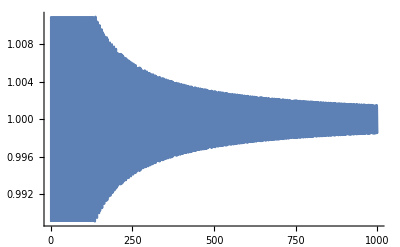

```mathematica
Plot[%138,{T,0,1000}]
```

```mathematica
-Integrate [Sin[τ]Sin[θ]Cos[τ+θ],{τ,-T,T},{θ,-T,T}]/T^2
```

(T-sin(T) cos(T))^2/T^2

```mathematica
MatrixExp[I{τ ,θ ,μ }.pvec]
```

((ⅇ^(√(-θ^2-μ^2-τ^2)) (ⅈ μ+√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (ⅈ μ-√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2)) | (ⅇ^(√(-θ^2-μ^2-τ^2)) (θ+ⅈ τ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (θ+ⅈ τ))/(2 √(-θ^2-μ^2-τ^2))
(ⅇ^(√(-θ^2-μ^2-τ^2)) (ⅈ τ-θ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (ⅈ τ-θ))/(2 √(-θ^2-μ^2-τ^2)) | (ⅇ^(√(-θ^2-μ^2-τ^2)) (√(-θ^2-μ^2-τ^2)-ⅈ μ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (-ⅈ μ-√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2)))

```mathematica
I{τ ,θ ,μ }.pvec
```

(ⅈ μ | ⅈ (τ-ⅈ θ)
ⅈ (ⅈ θ+τ) | -ⅈ μ)

```mathematica
MatrixE
```

```mathematica
MatrixExp[%]
```

((ⅇ^(√(-θ^2-μ^2-τ^2)) (ⅈ μ+√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (ⅈ μ-√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2)) | (ⅇ^(√(-θ^2-μ^2-τ^2)) (θ+ⅈ τ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (θ+ⅈ τ))/(2 √(-θ^2-μ^2-τ^2))
(ⅇ^(√(-θ^2-μ^2-τ^2)) (ⅈ τ-θ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (ⅈ τ-θ))/(2 √(-θ^2-μ^2-τ^2)) | (ⅇ^(√(-θ^2-μ^2-τ^2)) (√(-θ^2-μ^2-τ^2)-ⅈ μ))/(2 √(-θ^2-μ^2-τ^2))-(ⅇ^(-√(-θ^2-μ^2-τ^2)) (-ⅈ μ-√(-θ^2-μ^2-τ^2)))/(2 √(-θ^2-μ^2-τ^2)))

```mathematica
FullSimplify[MatrixExp[I{τ ,θ ,μ }.pvec],{τ ,θ ,μ }∈Reals]
```

(cosh(√(-θ^2-μ^2-τ^2))+(ⅈ μ sinh(√(-θ^2-μ^2-τ^2)))/(√(-θ^2-μ^2-τ^2)) | ((θ+ⅈ τ) sinh(√(-θ^2-μ^2-τ^2)))/(√(-θ^2-μ^2-τ^2))
-((θ-ⅈ τ) sinh(√(-θ^2-μ^2-τ^2)))/(√(-θ^2-μ^2-τ^2)) | cosh(√(-θ^2-μ^2-τ^2))-(ⅈ μ sinh(√(-θ^2-μ^2-τ^2)))/(√(-θ^2-μ^2-τ^2)))

```mathematica
f3[{1,0,0},{0,1,0},{0,0,1}]
```

(0 | 0
0 | 0)

```mathematica
f3[{1,0,0},{1,0,0},{0,0,1}]
```

((ⅈ ∫_-T^T ∫_-T^T ∫_-T^T ((ⅇ^(ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (μ+√(θ^2+2 τ θ+μ^2+τ^2)))/(2 √(θ^2+2 τ θ+μ^2+τ^2))-(ⅇ^(-ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (μ-√(θ^2+2 τ θ+μ^2+τ^2)))/(2 √(θ^2+2 τ θ+μ^2+τ^2))) sin(θ) sin(μ) sin(τ)ⅆμⅆθⅆτ)/T^3 | 0
0 | (ⅈ ∫_-T^T ∫_-T^T ∫_-T^T ((ⅇ^(ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (√(θ^2+2 τ θ+μ^2+τ^2)-μ))/(2 √(θ^2+2 τ θ+μ^2+τ^2))-(ⅇ^(-ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (-μ-√(θ^2+2 τ θ+μ^2+τ^2)))/(2 √(θ^2+2 τ θ+μ^2+τ^2))) sin(θ) sin(μ) sin(τ)ⅆμⅆθⅆτ)/T^3)

```mathematica
f3[{1,0,0},{1,0,0},{0,1,0}]
```

(0 | (∫_-T^T ∫_-T^T ∫_-T^T (ⅇ^(-ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (-1+ⅇ^(2 ⅈ √(θ^2+2 τ θ+μ^2+τ^2))) (θ-ⅈ μ+τ) sin(θ) sin(μ) sin(τ))/(√(θ^2+2 τ θ+μ^2+τ^2))ⅆμⅆθⅆτ)/(2 T^3)
(∫_-T^T ∫_-T^T ∫_-T^T (ⅇ^(-ⅈ √(θ^2+2 τ θ+μ^2+τ^2)) (-1+ⅇ^(2 ⅈ √(θ^2+2 τ θ+μ^2+τ^2))) (θ+ⅈ μ+τ) sin(θ) sin(μ) sin(τ))/(√(θ^2+2 τ θ+μ^2+τ^2))ⅆμⅆθⅆτ)/(2 T^3) | 0)

```mathematica
(* ------------------ *)
```

```mathematica
MatrixExp[I(τ A+ θ B+μ Cm)]
```

((ⅇ^(√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (ⅈ (√3 θ-√3 μ)+2 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ))-(ⅇ^(-√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (ⅈ (√3 θ-√3 μ)-2 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) | (ⅈ ⅇ^(√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (-θ-μ+2 τ))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ))-(ⅈ ⅇ^(-√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (-θ-μ+2 τ))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ))
(ⅈ ⅇ^(√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (-θ-μ+2 τ))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ))-(ⅈ ⅇ^(-√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (-θ-μ+2 τ))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) | (ⅇ^(√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (ⅈ (√3 μ-√3 θ)+2 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ))-(ⅇ^(-√(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)) (ⅈ (√3 μ-√3 θ)-2 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)))/(4 √(-θ^2+μ θ+τ θ-μ^2-τ^2+μ τ)))

```mathematica
FullSimplify[%]
```

((2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ) cosh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ))+ⅈ √3 (θ-μ) sinh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)))/(2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)) | -(ⅈ (θ+μ-2 τ) sinh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)))/(2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ))
-(ⅈ (θ+μ-2 τ) sinh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)))/(2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)) | (2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ) cosh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ))-ⅈ √3 (θ-μ) sinh(√(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)))/(2 √(-θ^2+(μ+τ) θ-μ^2-τ^2+μ τ)))

```mathematica
f[t_]:=Chop[NIntegrate[Sin[τ ] Sin[θ] Sin[μ] %51,{τ,-t,t},{θ,-t,t},{μ,-t,t}]/(t^3)];
```

```mathematica
f[999999999]
```

(-5.54318×10^-6-2.37077×10^-10 ⅈ | 0.+0.161489 ⅈ
0.+0.161489 ⅈ | -5.54318×10^-6+2.37077×10^-10 ⅈ)

```mathematica
twoProd=MatrixExp[I(τ A+ θ B)]
```

((ⅇ^(√(-θ^2+τ θ-τ^2)) (ⅈ √3 θ+2 √(-θ^2+τ θ-τ^2)))/(4 √(-θ^2+τ θ-τ^2))-(ⅇ^(-√(-θ^2+τ θ-τ^2)) (ⅈ √3 θ-2 √(-θ^2+τ θ-τ^2)))/(4 √(-θ^2+τ θ-τ^2)) | (ⅈ ⅇ^(√(-θ^2+τ θ-τ^2)) (2 τ-θ))/(4 √(-θ^2+τ θ-τ^2))-(ⅈ ⅇ^(-√(-θ^2+τ θ-τ^2)) (2 τ-θ))/(4 √(-θ^2+τ θ-τ^2))
(ⅈ ⅇ^(√(-θ^2+τ θ-τ^2)) (2 τ-θ))/(4 √(-θ^2+τ θ-τ^2))-(ⅈ ⅇ^(-√(-θ^2+τ θ-τ^2)) (2 τ-θ))/(4 √(-θ^2+τ θ-τ^2)) | (ⅇ^(√(-θ^2+τ θ-τ^2)) (2 √(-θ^2+τ θ-τ^2)-ⅈ √3 θ))/(4 √(-θ^2+τ θ-τ^2))-(ⅇ^(-√(-θ^2+τ θ-τ^2)) (-ⅈ √3 θ-2 √(-θ^2+τ θ-τ^2)))/(4 √(-θ^2+τ θ-τ^2)))

```mathematica
g[t_]:=Chop[NIntegrate[Sin[τ ] Sin[θ]  twoProd,{τ,-t,t},{θ,-t,t}]/(t^2)];
```

```mathematica
Table[Quiet[g[i]],{i,1,10}]
```

({0.148232,0} | {0,0.148232}
{0.666636,0} | {0,0.666636}
{0.423419,0} | {0,0.423419}
{0.37739,0} | {0,0.37739}
{0.532123,0} | {0,0.532123}
{0.590089,0} | {0,0.590089}
{0.409539,0} | {0,0.409539}
{0.306172,0} | {0,0.306172}
{0.28709,0} | {0,0.28709}
{0.229721,0} | {0,0.229721})

```mathematica
Quiet[g[1000]]
```

(-0.000403618-2.20372×10^-6 ⅈ | 0.-0.000279006 ⅈ
0.-0.000279006 ⅈ | -0.000403618+2.20372×10^-6 ⅈ)

```mathematica
twoProd2=MatrixExp[I(τ {1,0,0}.pvec+ θ {1,0,0}.pvec)];
h[t_]:=Quiet[Chop[NIntegrate[Sin[τ ] Sin[θ]  twoProd2,{τ,-t,t},{θ,-t,t}]/(t^2)]];
```

```mathematica
Table[h[i],{i,6}]
```

({-0.297408,0} | {0,-0.297408}
{-1.4142,0} | {0,-1.4142}
{-1.09531,0} | {0,-1.09531}
{-0.767955,0} | {0,-0.767955}
{-1.11176,0} | {0,-1.11176}
{-1.09143,0} | {0,-1.09143})

```mathematica
Integrate[Cos[x]Cos[x],x]
```

x/2+1/4 sin(2 x)

```mathematica
∫cos(2cos(x))ⅆx
```

∫cos(2 cos(x))ⅆx

```mathematica
Integrate[r Sin[r Cos[ϕ]]Sin[r Sin[ϕ]]Cos[r],{r,0,R}]
```

1/16 ((csc^2(ϕ/2) (2 R (cot(ϕ/2)+1) sin(R (sin(ϕ)-cos(ϕ)+1))+csc^2(ϕ/2) cos(R (sin(ϕ)-cos(ϕ)+1))))/(cot(ϕ/2)+1)^2-(csc^2(ϕ/2) (2 R (cot(ϕ/2)-1) sin(R (sin(ϕ)+cos(ϕ)-1))+csc^2(ϕ/2) cos(R (sin(ϕ)+cos(ϕ)-1))))/(cot(ϕ/2)-1)^2-(sec^2(ϕ/2) (2 R (tan(ϕ/2)+1) sin(R (sin(ϕ)+cos(ϕ)+1))+sec^2(ϕ/2) cos(R (sin(ϕ)+cos(ϕ)+1))))/(tan(ϕ/2)+1)^2+(sec^2(ϕ/2) (sec^2(ϕ/2) cos(R (-sin(ϕ)+cos(ϕ)+1))-2 R (tan(ϕ/2)-1) sin(R (-sin(ϕ)+cos(ϕ)+1))))/(tan(ϕ/2)-1)^2)+1/16 ((csc^4(ϕ/2))/(cot(ϕ/2)-1)^2-(csc^4(ϕ/2))/(cot(ϕ/2)+1)^2-(sec^4(ϕ/2))/(tan(ϕ/2)-1)^2+(sec^4(ϕ/2))/(tan(ϕ/2)+1)^2)

```mathematica
Integrate[%30,{ϕ,0, 2Pi}]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of TraditionalForm`cos(R\ (cos(ϕ) + sin(ϕ) - 1))\ csc^4(ϕ/2)/16\ (cot(ϕ/2) - 1)^2 - csc^4(ϕ/2)/16\ (cot(ϕ/2) - 1)^2 + cos(R\ (-cos(ϕ) + sin(ϕ) + 1))\ csc^4(ϕ/2)/16\ (cot(ϕ/2) + 1)^2 - csc^4(ϕ/2)/16\ (cot(ϕ/2) + 1)^2 + R\ sin(R\ (-cos(ϕ) + sin(ϕ) + 1))\ csc^2(ϕ/2)/8\ (cot(ϕ/2) + 1)^2 + « 9 » + R\ sec^2(ϕ/2)\ sin(R\ (cos(ϕ) - sin(ϕ) + 1))/8\ (tan(ϕ/2) - 1)^2 + cos(R\ (cos(ϕ) + sin(ϕ) + 1))\ sec^4(ϕ/2)/16\ (tan(ϕ/2) + 1)^2 - sec^4(ϕ/2)/16\ (tan(ϕ/2) + 1)^2 + R\ sec^2(ϕ/2)\ sin(R\ (cos(ϕ) + sin(ϕ) + 1))/8\ (tan(ϕ/2) + 1)^2 + R\ sec^2(ϕ/2)\ sin(R\ (cos(ϕ) + sin(ϕ) + 1))\ tan(ϕ/2)/8\ (tan(ϕ/2) + 1)^2 does not converge on TraditionalForm`{0, 2\ π}.

∫_0^(2 π) (1/16 ((csc^2(ϕ/2) (2 R (cot(ϕ/2)+1) sin(R (sin(ϕ)-cos(ϕ)+1))+csc^2(ϕ/2) cos(R (sin(ϕ)-cos(ϕ)+1))))/(cot(ϕ/2)+1)^2+(csc^2(ϕ/2) (2 R (cot(ϕ/2)-1) sin(R (sin(ϕ)+cos(ϕ)-1))+csc^2(ϕ/2) cos(R (sin(ϕ)+cos(ϕ)-1))))/(cot(ϕ/2)-1)^2+(sec^2(ϕ/2) (2 R (tan(ϕ/2)+1) sin(R (sin(ϕ)+cos(ϕ)+1))+sec^2(ϕ/2) cos(R (sin(ϕ)+cos(ϕ)+1))))/(tan(ϕ/2)+1)^2+(sec^2(ϕ/2) (sec^2(ϕ/2) cos(R (-sin(ϕ)+cos(ϕ)+1))-2 R (tan(ϕ/2)-1) sin(R (-sin(ϕ)+cos(ϕ)+1))))/(tan(ϕ/2)-1)^2)+1/16 (-(csc^4(ϕ/2))/(cot(ϕ/2)-1)^2-(csc^4(ϕ/2))/(cot(ϕ/2)+1)^2-(sec^4(ϕ/2))/(tan(ϕ/2)-1)^2-(sec^4(ϕ/2))/(tan(ϕ/2)+1)^2))ⅆϕ

```mathematica
Integrate[Cos[r Cos[ϕ]]Cos[r Sin[ϕ]]Cos[r],{ϕ,0,2 Pi}]
```

∫_0^(2 π) cos(r) cos(r cos(ϕ)) cos(r sin(ϕ))ⅆϕ

```mathematica
(*----------------------------------------------- *)
f3[a1_,a2_,a3_]:=Integrate [Sin[τ]Sin[θ]Sin[μ] MatrixExp[I(τ a1.pvec+ θ a2.pvec+μ a3.pvec)],{τ,-T,T},{θ,-T,T},{μ,-T,T}]/T^3;
```

```mathematica
Sinc[x]
```

```mathematica
a={1,0,0};b={-1/2,0,√3/2}; c={-1/2,0,-√3/2};
```

```mathematica
a={a1,a2,a3}; b={b1,b2,b3};c={c1,c2,c3};
```

```mathematica
a={1,0,0};b={-1/2,1/2,1/√2}; c={-1/2,0,-√3/2};
```

```mathematica
FullSimplify[√((x a + y b + z c).(x a + y b + z c))]
```

√((a1 x+b1 y+c1 z)^2+(a2 x+b2 y+c2 z)^2+(a3 x+b3 y+c3 z)^2)

```mathematica
Integrate [Sin[x]Sin[y]Sin[z] Cos[Norm[x a + y b + z c]],{x,-T,T},{y,-T,T},{z,-T,T}]/T^3
```

(∫_-T^T ∫_-T^T ∫_-T^T sin(x) sin(y) sin(z) cos(√(x^2-x (y+z)+y^2-y z+z^2))ⅆzⅆyⅆx)/T^3

```mathematica
Integrate [x Sin[x]Sin[y]Sin[z] Sinc[Norm[x a + y b + z c]],{x,-T,T},{y,-T,T},{z,-T,T}]/T^3
```

```mathematica
a=b=c={1,0,0};
```

```mathematica
a={1,0,0};b={0,1,0};c={0,0,1};
```

```mathematica
a={1,0,0};b={1,1,0}/√2;c={0,1,0};
```

```mathematica
a={1,0,0};b={1,0,0};c={0,1,0};
```

```mathematica
a={1,0,0};b={-1/2,0,√3/2}; c={-1/2,0,-√3/2};
```

```mathematica
f[5Pi]
```

{0,0.00960363,0}

```mathematica
DeleteDuplicates[{0,0.00960363283070216,0}]
```

{0,0.00960363}

```mathematica
g[a,b,c]
```

{0.,0.166667,0.}

```mathematica
f[4 Pi]
```

{0.158455,-0.0779589,0}

```mathematica
f[Pi]
```

{0.175234,0.198447,0}

```mathematica
a={1,0,0};b={√3/2,1/2,0}; c={3/5,4/5,0};
```

```mathematica
Norm[x a + y b + z c]
```

√(Abs[x+(√3 y)/2+(3 z)/5]^2+Abs[y/2+(4 z)/5]^2)

```mathematica
f
```

```mathematica
√-4
```

2 ⅈ

```mathematica
FullSimplify[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)]
```

√((x+y+z)^2)

```mathematica
√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)
```

√(x^2+2 x y+2 x z+y^2+2 y z+z^2)

```mathematica
f[T_]:=Chop[NIntegrate[-Sin[x]Sin[y]Sin[z]  Sin[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)]Normalize[(x a + y b + z c)],{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3)];
```

```mathematica
f2[Pi]
```

{1.,0,0}

```mathematica
fsame1[T_]:=NIntegrate[-Sin[x]Sin[y]Sin[z]  Sinc[x+y+z](x a + y b + z c),{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3);
```

```mathematica
fsame2[T_]:=NIntegrate[-Sin[x]Sin[y]Sin[z]  Sin[x+y+z](x a + y b + z c)/(x+y+z),{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3);
```

```mathematica
len=35;Plot3D[Sin[x]Sin[y]  Sin[x  +y],{x,-len,len},{y,-len,len}]
```

-Graphics3D-

```mathematica
fsame[T_]:=NIntegrate[-Sin[x]Sin[y]Sin[z]  Sin[x+y+z],{x,-T,T},{y,-T,T},{z,-T,T}]/( T^3);
```

```mathematica
Integrate[Sin[x]Sin[y]Sin[z]  Sinc[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)](x a + y b + z c),{x,-T,T},{y,-T,T},{z,-T,T}]
```

$Aborted

```mathematica
Integrate[Sin[x]Sin[y]Sin[z]  Sinc[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)](x a + y b + z c),{x,-T,T},{y,-T,T},{z,-T,T}]
```

```mathematica
Integrate[Sin[x]Sin[y]Sin[z]  Sinc[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)]x,{x,0,T},{y,-T,T},{z,-T,T}]
```

```mathematica
fsame[Pi]
```

1.

```mathematica
fsame1[Pi]
```

{0.662199,0.,0.}

```mathematica
fsame2[Pi]
```

{1.,0.,0.}

```mathematica
f[Pi]
```

{1.,0,0}

```mathematica
Table[f[i Pi][[1]],{i,1,10}]
```

{0.662199,1.02546,0.00991541,0.356838,1.34617,0.10844,0.228511,1.53193,0.307998,0.18239}

```mathematica
f[133Pi]
```

{1.37635,0.,0.}

```mathematica
f[1000]
```

{0.00381754,0,0}

```mathematica
f[1001]
```

{-0.00156216,-0.000823926,0}

```mathematica
N[b]
```

{-0.5,0.5,0.707107}

```mathematica
N[c]
```

{-0.5,0.,-0.866025}

```mathematica
g[a_,b_,c_]:=N[(a.b)c +(a.c) b + (b.c)a]/3;
```

```mathematica
g[a,b,c]
```

{1.,0.,0.}

```mathematica
(* why so small in magnitude? might as well be zero *)
```

```mathematica
f[10^15]
```

{-0.000360456,0,0}

```mathematica
Normalize[%55]
```

{-0.907171,-0.420761,0.}

```mathematica
Normalize[%54]
```

{0.891974,0.452087,0.}

```mathematica
f[1]
```

{-0.0135834,-0.00683246,0}

```mathematica
f[4]
```

{-0.00394748,0,0}

```mathematica
f[100]
```

{0.00930871,0,0}

```mathematica
f[100.5]
```

{-0.000515609,-0.000314788,0}

```mathematica
f[1000.5]
```

{0.00901801,0,0}

```mathematica
f[999999.5]
```

{0.00409758,0,0}

```mathematica
f[999999999999.5]
```

{-0.00570116,0,0}

$Aborted

```mathematica
a={1,0,0};b={1,0,0};c={1,0,0};
```

```mathematica
ftry[T_]:=Chop[NIntegrate[- Sin[x]Sin[y]Sin[z]  Sin[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)] Norm[(x a + y b + z c)],{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3)];
```

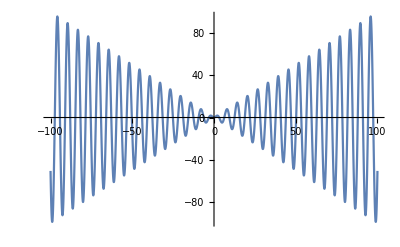

```mathematica
Plot[x Sin[x], {x,-100,100}]
```

```mathematica
ftry[Pi]
```

-2.90258×10^-7

```mathematica
f[2 ]
```

{1.68177,0,0}

```mathematica
len=4;
```

```mathematica
h[x_,y_,z_]:=√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c);
```

```mathematica
ContourPlot3D[h[x,y,z],{x,-len,len},{y,-len,len},{z,-len,len}]
```

-Graphics3D-

```mathematica
(*------------------------ 
after many trials above, found that the best functions *)
```

```mathematica
a=b=c={1,0,0};
```

```mathematica
a={1,0,0};b={0,1,0};c={0,0,1};
```

```mathematica
a={1,0,0};b={1,1,0}/√2;c={0,1,0};
```

```mathematica
c={1,0,0};b={-1/2,0,√3/2}; a={-1/2,0,-√3/2};
```

```mathematica
ϵ=0.9;a=s2c[Pi/2,ϵ];b=s2c[Pi/2,2Pi/3+ϵ];c=s2c[Pi/2,4Pi/3+ϵ];
```

```mathematica
a=s2c[0.8 Pi/2, 4]; b=s2c[0.2 , Pi-1]; a=s2c[1, 2];  (* arbitrary orientation *)
```

```mathematica
f[T_]:=Quiet[Chop[NIntegrate[-Sin[x]Sin[y]Sin[z]  Sin[√(x^2+y^2+z^2+2 x y a.b +2 x z a.c + 2 y z b.c)]Normalize[(x a + y b + z c)],{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3)]];
```

```mathematica
ftri[T_]:=Quiet[Chop[NIntegrate[-Sin[x]Sin[y]Sin[z]  Sin[√(x^2+y^2+z^2- x y - x z- y z)]Normalize[(x a + y b + z c)],{x,-T,T},{y,-T,T},{z,-T,T}]/(T^3)]];
```

```mathematica
ftri[2]
```

{0.00274088,0,1/8 NIntegrate[-(sin(x) ((√3 y)/2-(√3 z)/2) sin(y) sin(z) sin(√(x^2-x y-x z+y^2-y z+z^2)))/(√(Abs[x-y/2-z/2]^2+Abs[(√3 y)/2-(√3 z)/2]^2)),{x,-2,2},{y,-2,2},{z,-2,2}]}

```mathematica
f[Pi+1]
```

```mathematica
{-0.03169646923599942,0,-0.054899895137294985}
```

```mathematica
f[1000000000
```

```mathematica
listf[T_]:=Table[f[T+0.02 i],{i,0,10}]
```

```mathematica
listf[1000]
```

(-0.00227866 | 0.00552574 | 0.00489968
-0.00318702 | 0.00585274 | 0.00523949
-0.00330468 | 0.00681727 | 0.00547588
-0.00347422 | 0.00700674 | 0.00552517
-0.00394294 | 0.00920254 | 0.00605377
-0.0045029 | 0.0100778 | 0.00664242
-0.00487189 | 0.0113534 | 0.00733165
-0.0052889 | 0.0125055 | 0.00832537
-0.00582343 | 0.0136806 | 0.00832199
-0.00660246 | 0.014816 | 0.0100929
-0.005686 | 0.0161278 | 0.0112603)

```mathematica
listf[10^10]
```

(-0.0934281 | 0 | 0
-0.0969578 | 0 | 0
-0.103061 | 0 | 0
-0.105248 | 0 | 0
-0.112348 | 0 | 0
-0.11403 | 0 | 0
-0.120949 | 0 | 0
-0.127749 | 0 | 0
-0.129015 | 0 | 0
-0.130937 | 0 | 0
-0.130304 | 0 | 0)

```mathematica
listf[10^16+.5]
```

(0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0
0.00400165 | 0 | 0)

```mathematica
listf[10^17]
```

(0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9
0.000410868 | 0 | 3.70689×10^-9)

```mathematica
f[200000016.7]
```

{0.821727,0,0}

```mathematica
(* symmetrization *)
g[a_,b_,c_]:=N[(a.b)c +(a.c) b + (b.c)a]/3;
```

```mathematica
(* found that 
-f converges as expected (if you define it as above) for a=b=c
- f generally diverges
- f seems to be zero in the entries where g is zero ... which motivated me to show analytically that they are equal....
Allahuma laka al7amd *)
```

```mathematica
T=Pi;Integrate[x Sin[x],{x,-T,T}]/T
```

```mathematica
Clear[T]
```

```mathematica
FullSimplify[Integrate[x^3 Sin[x],{x,-T,T}]/T]
```

(6 (T^2-2) sin(T))/T-2 (T^2-6) cos(T)

```mathematica
(* still factor of 2 *)
```

```mathematica
Integrate[Sinc[x],x]
```

x

```mathematica
7.2 10^-7 4.79 10^14 √(300/20)
```

1.33571×10^9

```mathematica
(* --------------------- *)
```

```mathematica
d1=0.8;d2=0.6;
```

```mathematica
2 d1^2-1
```

0.28

```mathematica
d1^2+d2^2
```

```mathematica
1.
```

```mathematica
len=30;
```

```mathematica
Plot
```

```mathematica
Plot3D
```

```mathematica
a=-.7;d1=√((1+a)/2); d2=√((1-a)/2);Plot3D[(Cos[v/d1]-Cos[u/d2])Cos[√(u^2+v^2)],{u,-len,len},{v,-len,len}(*,RegionFunction->Function[{u,v},v/(d1+.01)≤-u/d2 *)],PlotPoints->25,MaxRecursion->4]
```

-Graphics3D-

```mathematica
len=20; Manipulate[d1=√((1+a)/2); d2=√((1-a)/2); Plot3D[(Cos[v/d1]-Cos[v/d2])Cos[√(u^2+v^2)],{u,-len,len},{v,-len,len},PlotPoints->25,MaxRecursion->4],{{a,0},-.999,.999}]
```

Plot3D::plln: Limiting value TraditionalForm`-len in TraditionalForm`{u, -len, len} is not a machine-sized real number.

```mathematica
f[a_,T_]:=Module[{d1,d2},
d1=√((1+a)/2); d2=√((1-a)/2);
Quiet[Chop[NIntegrate[(Cos[v/d1]-Cos[v/d2])Cos[√(u^2+v^2)],{u,-T,T},{v,-T,T}]/(T^2)]]
]
```

```mathematica
f[0,1]
```

0

```mathematica
f[.999,100]
```

0.117703

```mathematica
Integrate[Cos[3Cos[θ]],θ]
```

∫cos(3 cos(θ))ⅆθ

```mathematica
(*---------------*)
```

```mathematica
Clear[a,b,c]
```

```mathematica
a(-x+y+z)^2+b(x-y+z)^2+(1-a-b)(x+y-z)^2
```

(-a-b+1) (x+y-z)^2+a (-x+y+z)^2+b (x-y+z)^2

```mathematica
Expand[%]
```

-4 a x y+4 a y z-4 b x y+4 b x z+x^2+2 x y-2 x z+y^2-2 y z+z^2